```mathematica
Get[StringJoin[NotebookDirectory[],"PlaneCurvePlot.wl"]]
```

## Normal

#### (* Parabola and its evolute Semi-cubic parabola *)

```mathematica
PlaneCurvePlot[{t,t^2},{t,-3,3,.1},NormalLineLength->15,NormalLineStyle->{Hue[0]},PlotDot->False,AspectRatio->Automatic,PlotRange->{{-6,6},{-2,5}}]
```

-Graphics-

#### (* two Astroids*)

```mathematica
PlaneCurvePlot[{(3 Cos[t])/4+1/4 Cos[3 t],(3 Sin[t])/4-1/4 Sin[3 t]},{t,0,2 π,(2 π)/80},NormalLineLength->3,CurveStyle->{Thickness[.007]},PlotRange->All,AspectRatio->Automatic,Axes->False]
```

-Graphics-

```mathematica
(* Cardioid *)
```

```mathematica
PlaneCurvePlot[{2 Cos[t]+Cos[2 t],2 Sin[t]+Sin[2 t]},{t,0,2 π,(2 π)/40},SecantConnection->{8,1},NormalLineLength->5,CurveStyle->{Thickness[.007]},AspectRatio->Automatic,PlotRange->{{-2.5,4},{-3.6,3.6}}]
```

-Graphics-

#### (* Archimedes' Spiral and its normal *)

```mathematica
PlaneCurvePlot[{t Cos[t],t Sin[t]},{t,0,4 π,.2},NormalLineLength->6,PlotDot->False,PlotRange->All,AspectRatio->Automatic]
```

-Graphics-

#### (* Ellipse and its Evolute *)

```mathematica
PlaneCurvePlot[{Cos[t],0.6 Sin[t]},{t,0,2 π,(2 π)/60},NormalLineLength->8,PlotDot->False,NormalLineStyle->{Hue[0,0,0]},CurveColorFunction->{Hue},CurveStyle->{Thickness[.007]},AspectRatio->Automatic,PlotRange->{{-2,2},{-2,2}}]
```

-Graphics-

#### (* deltoid normal beauty *)

```mathematica
PlaneCurvePlot[{(2 Cos[t])/3+1/3 Cos[2 t],(2 Sin[t])/3-1/3 Sin[2 t]},{t,0,2 π,(2 π)/120},NormalLineLength->1,PlotDot->False,SecantConnection->{60,1},Axes->False,AspectRatio->Automatic]
```

-Graphics-

#### (* Hypotrochoid normal beauty, {1,5/14,4/7} *)

```mathematica
PlaneCurvePlot[{(9 Cos[t])/14+4/7 Cos[(9 t)/5],(9 Sin[t])/14-4/7 Sin[(9 t)/5]},{t,0,5 2 π,(5 2 π)/140},NormalLineLength->1,Axes->False,AspectRatio->Automatic]
```

-Graphics-

#### (* hypotrochoid normal beauty, [1, 8/15, 8/15] *)

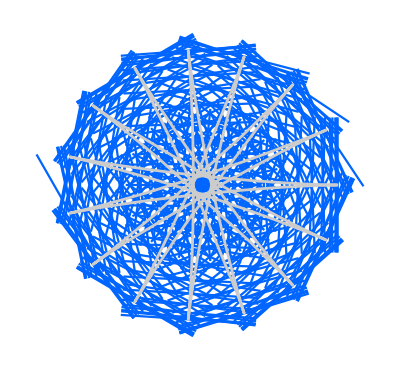

```mathematica
PlaneCurvePlot[{8/15 Cos[(7 t)/8]+(7 Cos[t])/15,-8/15 Sin[(7 t)/8]+(7 Sin[t])/15},{t,0,8 2 π,(8 2 π)/(15 20)},NormalLineLength->1,CurveColorFunction->{GrayLevel[.8]&},Axes->False,PlotDot->False,AspectRatio->Automatic]
```

#### (* "Cactus" *)

```mathematica
PlaneCurvePlot[t Cos[t]*{Cos[0.45* π* Cos[t]],Sin[0.45* π* Cos[t]]},{t,0,4.5 π,.05},NormalLineLength->.5,PlotCurve->True,PlotDot->False,AspectRatio->Automatic]
```

-Graphics-